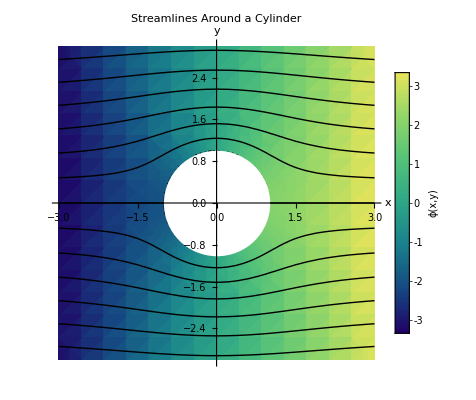

```mathematica
Subscript[U, 0]=1;
a=1;
ϕ[x_,y_]=Subscript[U, 0](x+(a^2 x)/(x^2+y^2));
ψ[x_,y_]=Subscript[U, 0](y-(a^2 y)/(x^2+y^2));
ϕPlot=DensityPlot[ϕ[x,y],{x,-3,3},{y,-3,3},
RegionFunction->Function[{x,y},x^2+y^2>a^2],
ColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,LegendLabel->"ϕ(x,y)"]];
ψPlot=ContourPlot[ψ[x,y],{x,-3,3},{y,-3,3},
RegionFunction->Function[{x,y},x^2+y^2>a^2],
ContourShading->None,
Contours->25];
Ω=Graphics[{White,Disk[{0,0},a+0.01]}];
Show[ϕPlot,ψPlot,Ω,
PlotLabel->"Streamlines Around a Cylinder",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
```

```mathematica
f[z_]=U0(z + α^2/z);
ComplexExpand[f[x+ⅈ y]]
```

U0 x+(U0 x α^2)/(x^2+y^2)+ⅈ (U0 y-(U0 y α^2)/(x^2+y^2))